```mathematica
(* constants*)
(*https://en.wikipedia.org/wiki/Avogadro_constant*)
N0=6.02214076*10^23;
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
(*single monopole charge*)
Qm=2*Pi*hbar/e;
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
α=1/137.035999206;
αw=0.42541281596347497;
(*From:https://en.wikipedia.org/wiki/Fermi%27s_interaction*)
Gf=1.4327038609285911*^-49;
Ω=0.0078749969978123844;
kb=1.380658*10^(-16);
omega=0.00787499699;
mH=126*10^3*me/mev;
mp=1.672621777*10^(-24);
mn=1838.6402*me;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
θwrad=ArcSin[Sqrt[0.231208]];
θwdeg=θwrad*180/Pi;
(*https://en.wikipedia.org/wiki/Precision_tests_of_QED*)
g=2*1.00115965218085;
(* unification mass:anti-deSitter model*)
muni=3.6543166832631125*^-12;
mtau=1776.82*me/mev;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=126*10^3*me/mev;
mz=91.1876*10^3*me/mev;
mw=80.4335*10^3*me/mev;
mtop=172.76*10^3*me/mev;
mbottom=4.1*10^3*me/mev;
mcharm=1.275*10^3*me/mev;
mstrange=92.4*me/mev;
momegassb=6054.4/10^3;
mplanck=Sqrt[hbar*c/G];
mup=2.01*me/mev;
md0=4.79*me/mev;
(* log linear fit for 4th level quarks*)
mwhite=1.1677931388727855*^-19;
mblack=1.8611487827001873*^-22;
mout=1.5020666505936996*^-20;
Tvac=2.72548;
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2;
rplanck=2*Pi*hbar/(mplanck*c);
tplanck=rplanck/c;
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
mnu=1.78266270 * 10^(-33 );
mnumu=6.7978246932973695*^-31;
mnutau=1.1431743145263108*^-29;
(*Weak charge on 5d simplex*)
Cw=(3!*2!)*Det[{{α,0,0,0,0,1},{0,α,0,0,0,1},{0,0,α,0,0,1},{0,0,0,α,0,1},{0,0,0,0,α,1},{0,0,0,0,0,1}}]/5!;
rw=Cw^2/(mnu*c^2);
(*http://www.bottomlayer.com/bottom/deutsch/neutrino.html*)
(* Weeks volume*)
vw=0.94270736277692772092;

(* Thurston-Meyerhoff volume*)
vt=0.981368828892232088914;
(*lepton hyperbolic 3 manifold volume*)
vl=(18/24)*vt;
pizero=134.9766*me/mev;
(* Bohr radius: https://en.wikipedia.org/wiki/Bohr_radius*)
ab=5.2917721067*10^(-9);
(*:https://en.wikipedia.org/wiki/Pion:*)
tpip=2.6033*10^(−8 );
tpiz=8.4*10^(−17);
(* product quarks masses in me*)
mup1=12.239779918021176;mdp1=12.256361761325056;
(* elliptic product quarks for Pi mesons*)
mupi=16.25229214603282;mdpi=16.805755043381577;
mqmu=Sqrt[mmu/me];
mqtau=Sqrt[mtau/me];
(* hadron strange and charm product quark masses*)
mqs=mqtau*mup1/mqmu;
mqc=2*mqs;
ttau=2.932*10^(−13);
tmu=2.1969811*10^(−6);
(*.10https://physicstoday.scitation.org/doi/10.1063/PT.3.4424*)
(*.10https://physics.stackexchange.com/questions/134856/units-of-hubble-time-and-hubble-constant*)
Hcbm=67.4/(3.09*10^19);
Hsnova=74.0/(3.09*10^19);
Hlense=73.3/(3.09*10^19);
Have=73.8/(3.09*10^19);
H0=2.2894835758225842*^-18;
th0=1/H0;
(* CMB age*)
tcmb=372000*365.25*24*60*60;
tsnova=1/Hsnova;
msun=1.9891*10^33;
(*first approximation electron g:single loop GED:weak g'*)
g0=2*(1+α/2);
Clear[g1]
g1=g1/.Solve[(g1/Sqrt[g+g1^2])^2==0.231208,g1][[2]];
(* gravity momemt γ*)
γ=e*G/(hbar*c);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(* anomalous magnetic moment of electron:https://en.wikipedia.org/wiki/Anomalous_magnetic_dipole_moment*)
ae=0.0015865218059;
```

```mathematica
(* geometricn Average of masses*)
```

```mathematica
m0=Sqrt[(mz*mhiggs)]
```

1.91083×10^-22

```mathematica
mh0=mhiggs/m0
```

1.17549

```mathematica
mz0=mz/m0
```

0.850712

```mathematica
p[x_]=ExpandAll[(x-mh0)*(x+mh0)*(x-I*mz0)*(x+I*mz0)]
```

(-1.+0. ⅈ)-(0.658056+0. ⅈ) x^2+x^4

```mathematica
-1-(mhiggs x^2)/mz+(mz x^2)/mhiggs+x^4
```

-1-0.658056 x^2+x^4

```mathematica
(-1.0000000000000004+0. ⅈ)-(0.6580557080616712+0. ⅈ) x^2+x^4
```

(-1.+0. ⅈ)-(0.658056+0. ⅈ) x^2+x^4

```mathematica
x/.Solve[D[p[x],{x,2}]==0,x][[2]]
```

0.331174

```mathematica
(*Solve[(√(mhiggs^2-mz^2))/(√6 √mhiggs √mz)==1/3,mhiggs]*)
```

Solve::ivar: 2.24615×10^-22 is not a valid variable.

Solve[False,2.24615×10^-22]

```mathematica
mhiggs/(2.255353113693151*^-22)
```

0.995921

```mathematica
{{mhiggs->1/3 (mz-√10 mz)},{mhiggs->1/3 (mz+√10 mz)}}
```

{{2.24615×10^-22→-1.17164×10^-22},{2.24615×10^-22→2.25535×10^-22}}

```mathematica
Sqrt[λ]/.Solve[0.3311735969904785==mhiggs/Sqrt[λ],λ][[1]]
```

6.78241×10^-22

```mathematica
{{λ->4.600103653518404*^-43}}
```

{{λ→4.6001×10^-43}}

```mathematica
p[x]/.Solve[D[p[x],{x,2}]==0,x]
```

{-1.06014+0. ⅈ,-1.06014+0. ⅈ}

```mathematica
(*Mexican hat plot*)
```

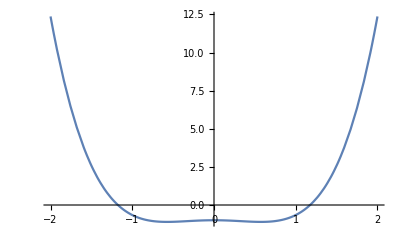

```mathematica
Plot[p[x],{x,-2,2}]
```

```mathematica
ExpandAll[(-1.1754857800810619+x) ((0.-0.8507121199977765 ⅈ)+x) ((0.+0.8507121199977765 ⅈ)+x) (1.1754857800810619+x)]//Chop
```

-1.-0.658056 x^2+x^4

```mathematica
CoefficientList[p[x],x]//Chop
```

{-1.,0,-0.658056,0,1}

```mathematica
CoefficientList[-0.9492760829938066 .10+(0.+1.1304771383544785 ⅈ) x-(0.+1.1304771383544785 ⅈ) .10 x-1.346266468983048 x^2+0.7051175267782442 .10 x^2-(0.+0.839712764448799 ⅈ) x^3+(0.+0.839712764448799 ⅈ) .10 x^3+x^4,x]
```

{-0.949276 .10,(0.+1.13048 ⅈ)-(0.+1.13048 ⅈ) .10,-1.34627+0.705118 .10,(0.-0.839713 ⅈ)+(0.+0.839713 ⅈ) .10,1}

```mathematica
1/(mhiggs+mz)^4(-16 .10 mhiggs^2 mz^2+8 ⅈ mhiggs^3 mz x-8 ⅈ .10 mhiggs^3 mz x+8 ⅈ mhiggs^2 mz^2 x-8 ⅈ .10 mhiggs^2 mz^2 x-4 mhiggs^4 x^2-8 mhiggs^3 mz x^2-4 mhiggs^2 mz^2 x^2+4 .10 mhiggs^2 mz^2 x^2+8 .10 mhiggs mz^3 x^2+4 .10 mz^4 x^2-2 ⅈ mhiggs^3 mz x^3+2 ⅈ .10 mhiggs^3 mz x^3-6 ⅈ mhiggs^2 mz^2 x^3+6 ⅈ .10 mhiggs^2 mz^2 x^3-6 ⅈ mhiggs mz^3 x^3+6 ⅈ .10 mhiggs mz^3 x^3-2 ⅈ mz^4 x^3+2 ⅈ .10 mz^4 x^3+mhiggs^4 x^4+4 mhiggs^3 mz x^4+6 mhiggs^2 mz^2 x^4+4 mhiggs mz^3 x^4+mz^4 x^4)
```

4.45025×10^85 (-2.13309×10^-86 .10+(0.+2.54026×10^-86 ⅈ) x-(0.+2.54026×10^-86 ⅈ) .10 x-3.02515×10^-86 x^2+1.58445×10^-86 .10 x^2-(0.+1.88689×10^-86 ⅈ) x^3+(0.+1.88689×10^-86 ⅈ) .10 x^3+2.24707×10^-86 x^4)

```mathematica
-(16 .10 mhiggs^2 mz^2)/(mhiggs+mz)^4+(8 ⅈ mhiggs^2 mz x)/(mhiggs+mz)^3-(8 ⅈ .10 mhiggs^2 mz x)/(mhiggs+mz)^3-(4 mhiggs^2 x^2)/(mhiggs+mz)^2+(4 .10 mz^2 x^2)/(mhiggs+mz)^2-(2 ⅈ mz x^3)/(mhiggs+mz)+(2 ⅈ .10 mz x^3)/(mhiggs+mz)+x^4
```

-0.949276 .10+(0.+1.13048 ⅈ) x-(0.+1.13048 ⅈ) .10 x-1.34627 x^2+0.705118 .10 x^2-(0.+0.839713 ⅈ) x^3+(0.+0.839713 ⅈ) .10 x^3+x^4

```mathematica
1/(mhiggs+mz)^4(mhiggs (-2+x)+mz x) (2 ⅈ .10 mz+(mhiggs+mz) x) (mhiggs x+mz (-2 ⅈ+x)) (mz x+mhiggs (2+x))
```

4.45025×10^85 (2.24615×10^-22 (-2+x)+1.62557×10^-22 x) ((0.+3.25113×10^-22 ⅈ) .10+3.87172×10^-22 x) (2.24615×10^-22 x+1.62557×10^-22 (-2 ⅈ+x)) (1.62557×10^-22 x+2.24615×10^-22 (2+x))

```mathematica
NSolve[p[x]==0,x]
```

{{x→-1.17549},{x→0.-0.850712 ⅈ},{x→0.+0.850712 ⅈ},{x→1.17549}}

```mathematica
ComplexPlot[p[x],{x,-2-I*2,2+I*2},ColorFunction->"CyclicReImLogAbs",ImageSize->Full,PlotPoints->50]
```

-Graphics-

```mathematica
Plot3D[Abs[p[x+I*y]],{x,-4,4},{y,-4,4},ColorFunction->"Rainbow",PlotPoints->50,ImageSize->Full]
```

-Graphics3D-